```mathematica
$MinPrecision=53;
```

### General Parameters

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10";
```

### Defining The Domains

#### u Domain(s)

u=1/r

```mathematica
prec=64;
```

```mathematica
uOuterMin=7/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=1;(*Number of outer subdomain*)
uOuterNodes=12;(*Number of points in each outer subdomains*)
uInnerNodes=20;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

```mathematica
InterfaceNodes//N
```

{0.7,1.1}

The function below gives an array containing arrays.
Each of these arrays is a subdomain that contains its relative points.

```mathematica
(*GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]*)
```

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
(*uValues=(*{{0.0,0.002025351319275129,0.00793732335844094,0.017256963302735746,0.02922924934990568,0.042884258086335746,0.05711574191366425,0.07077075065009432,0.08274303669726425,0.09206267664155907,0.09797464868072488,0.1},{0.09999999999999998,0.10144367836436871,0.10574782046109107,0.11283224826665475,0.12256499229529424,0.1347647499408149,0.1492042628011086,0.1656145500721956,0.1836899191516714,0.2030936601134971,0.22346431797684174,0.244422425928476,0.265577574071524,0.2865356820231582,0.30690633988650284,0.3263100808483286,0.3443854499278044,0.36079573719889135,0.37523525005918507,0.38743500770470574,0.3971677517333452,0.4042521795389089,0.40855632163563127,0.41000000000000003},{0.41,0.4114436783643687,0.41574782046109104,0.4228322482666548,0.4325649922952942,0.4447647499408149,0.4592042628011086,0.47561455007219555,0.4936899191516714,0.5130936601134971,0.5334643179768417,0.5544224259284759,0.5755775740715239,0.5965356820231582,0.6169063398865028,0.6363100808483285,0.6543854499278043,0.6707957371988913,0.685235250059185,0.6974350077047056,0.7071677517333451,0.7142521795389087,0.7185563216356312,0.72},{0.72,0.7214436783643687,0.7257478204610911,0.7328322482666547,0.7425649922952943,0.7547647499408149,0.7692042628011087,0.7856145500721956,0.8036899191516714,0.8230936601134972,0.8434643179768417,0.864422425928476,0.8855775740715239,0.9065356820231583,0.9269063398865028,0.9463100808483286,0.9643854499278044,0.9807957371988913,0.9952352500591851,1.0074350077047056,1.0171677517333453,1.0242521795389088,1.0285563216356313,1.03}}*)GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];*)
```

I call the function GetuDomain to define my u-grid.

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
1/(0.00477354380904716923912178181332651124503147387899328913971720272779107672699`64.)^4
```

1.92591160198105655706471132776633674500443597489942311285307944×10^9

```mathematica
uValues
```

{{0,0.004773543809047169239121781813326511245031473878993289139717202728,0.01896396540477786234311700000027046526166583904575378222406535256,0.04218418707772882501320083579135560897723853869444460367405473495,0.07380082171126224027335659771031824014855977894513537756736806256,0.1129514499309906238332471554265309985545680888299524501698504736,0.1585681446571505938508830386563340250773900755132234659702952862,0.2094066013714606898691054190900839967101425683511479976958644721,0.264080079500720297877198178771270305304860704231599251602573412,0.3210972290846836863898796230168959203054957279811735366848152299,0.3789027709153163136101203769831040796945042720188264633151847701,0.435919920499279702122801821228729694695139295768400748397426588,0.4905933986285393101308945809099160032898574316488520023041355279,0.5414318553428494061491169613436659749226099244867765340297047138,0.5870485500690093761667528445734690014454319111700475498301495264,0.6261991782887377597266434022896817598514402210548646224326319374,0.657815812922271174986799164208644391022761461305555396325945265,0.6810360345952221376568829999997295347383341609542462177759346474,0.6952264561909528307608782181866734887549685261210067108602827973,0.7},{0.7,0.7081014052771005220219263885867344601875090303155676089911009882,0.7317492934337637662276376702161264564973415003158924202714699765,0.7690278532109429871886149855067412893632417601326143144787408791,0.8169169973996227148941451701540753592951990179070926375147553335,0.8715370323453429719112414662767260662417897277748031343163834427,0.9284629676546570280887585337232739337582102722251968656836165573,0.9830830026003772851058548298459246407048009820929073624852446665,1.030972146789057012811385014493258710636758239867385685521259121,1.068250706566236233772362329783873543502658499684107579728530024,1.091898594722899477978073611413265539812490969684432391008899012,1.1}}

#### x Domain

X domain needs the extremals and the number of points

```mathematica
xMin=-750;
xMax=750;
xNodes=200;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-750,-1485/2,-735,-1455/2,-720,-1425/2,-705,-1395/2,-690,-1365/2,-675,-1335/2,-660,-1305/2,-645,-1275/2,-630,-1245/2,-615,-1215/2,-600,-1185/2,-585,-1155/2,-570,-1125/2,-555,-1095/2,-540,-1065/2,-525,-1035/2,-510,-1005/2,-495,-975/2,-480,-945/2,-465,-915/2,-450,-885/2,-435,-855/2,-420,-825/2,-405,-795/2,-390,-765/2,-375,-735/2,-360,-705/2,-345,-675/2,-330,-645/2,-315,-615/2,-300,-585/2,-285,-555/2,-270,-525/2,-255,-495/2,-240,-465/2,-225,-435/2,-210,-405/2,-195,-375/2,-180,-345/2,-165,-315/2,-150,-285/2,-135,-255/2,-120,-225/2,-105,-195/2,-90,-165/2,-75,-135/2,-60,-105/2,-45,-75/2,-30,-45/2,-15,-15/2,0,15/2,15,45/2,30,75/2,45,105/2,60,135/2,75,165/2,90,195/2,105,225/2,120,255/2,135,285/2,150,315/2,165,345/2,180,375/2,195,405/2,210,435/2,225,465/2,240,495/2,255,525/2,270,555/2,285,585/2,300,615/2,315,645/2,330,675/2,345,705/2,360,735/2,375,765/2,390,795/2,405,825/2,420,855/2,435,885/2,450,915/2,465,945/2,480,975/2,495,1005/2,510,1035/2,525,1065/2,540,1095/2,555,1125/2,570,1155/2,585,1185/2,600,1215/2,615,1245/2,630,1275/2,645,1305/2,660,1335/2,675,1365/2,690,1395/2,705,1425/2,720,1455/2,735,1485/2}

#### y Domain

```mathematica
yMin=-750;
yMax=750;
yNodes=xNodes;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues;
```

#### Grid

Here I define the grid. The first entry is for the number relative to the subdomain,2nd entry is the u-point, 3rd and 4th are for the x and y point. The outpout is the triplet that represent the point in the grid.

```mathematica
MyGrid=Table[{uValues[[i,u]],xValues[[x]],yValues[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid[[2,1,1,1]]//Dimensions
```

{3}

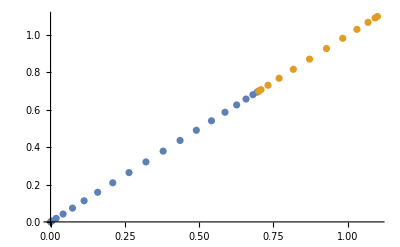

```mathematica
ListPlot[Table[{uValues[[i]],uValues[[i]]}//Transpose,{i,1,uValues//Length}]]
```

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

Here the goal is to intialise a boosted black brane in an inhomogeneous way, with noise created by a sum of sinusoidal functions each multiplied by small random coefficients

#### Random Factor

```mathematica
modesTot=2;(*Number of sinusoidals that build the noise*)
```

```mathematica
RandomModes1=Table[RandomInteger[{1,64}],{i,1,modesTot}](*Random Mode for u1*)
RandomModes2=Table[RandomInteger[{1,64}],{i,1,modesTot}](*Random Mode for u2*)
```

{37,28}

{33,56}

```mathematica
RandomModes1={12,29};
RandomModes2={42,48};
RandomModesy1={13,58};
RandomModesy2={20,34};
```

```mathematica
RandomCoefficients1=Table[Random[],{i,1,modesTot}](*Random Coefficients for u1*)
RandomCoefficients2=Table[Random[],{i,1,modesTot}](*Random Coefficients for u2*)
```

{0.955474,0.424098}

{0.687672,0.493808}

```mathematica
RandomCoefficients1={0.3574722145456855,0.8049967461264605};
RandomCoefficients2={0.11552499252714668,0.5472506362933037};
RandomCoefficientsy1={0.050914049685036246,0.669520107459068};
RandomCoefficientsy2={0.3525989113212813,0.6304108407889267};
```

```mathematica
RandomOffsetsy1=Table[Random[]2Pi,{i,1,modesTot}](*Random offset for u1*)
RandomOffsetsy2=Table[Random[]2Pi,{i,1,modesTot}](*Random offset for u2*)
```

{0.194763,2.92974}

{0.779876,2.09675}

```mathematica
RandomOffsets1={5.772098284647657,2.4120935314696124};
RandomOffsets2={2.2988527264495042,3.471687344793161};
RandomOffsetsy1={2.7019354914839884,2.2364904325714403};
RandomOffsetsy2={5.374373465607026,0.01855729769842717};
```

```mathematica
ClearAll[RandomFactor2]
```

Below I define the random factor that I will add to the profile of u1.

```mathematica
RandomFactor[{x_,y_}]=(*Sum[*)RandomCoefficients1[[1]] Cos[( RandomModes1[[1]]x+RandomModes1[[2]]y)2 Pi /(xMax-xMin)+RandomOffsets1[[1]]] (*+RandomCoefficients1[[i]] Sin[RandomModes2[[i]](i+1) 2 Pi (y(*{x,y}.RandomDirections[[i]]*))/(xMax-xMin)+RandomOffsets2[[i]]],{i,1,modesTot}]*);(*/;x<(xMax-xMin)/2&&y<(yMax-yMin)/2;
RandomFactor[{x_,y_}]=(Sum[RandomCoefficients[[i]] Cos[((i+2) 2 Pi ({x,y}.RandomDirections[[i]])/(xMax-xMin)-(xMax-xMin)/(2 Pi (i+1)) (RandomOffset-0.5))] ,{i,1,modesTot}])/;x>=(xMax-xMin)/2&&y<(yMax-yMin)/2;*)
```

```mathematica
NormFact=Max[Abs[(RandomFactor[{x,y}]//Minimize[#,{x,y}]&)[[1]]],(RandomFactor[{x,y}]//Maximize[#,{x,y}]&)[[1]]];(*This is a normalization factor*)
```

Below I define the random factor that I will add to the profile of u2.

```mathematica
RandomFactor2[{x_,y_}]=(*Sum[*)RandomCoefficientsy1[[1]] Cos[(RandomModesy1[[1]]x+RandomModesy1[[2]]y) 2 Pi /(xMax-xMin)+RandomOffsetsy1[[1]]] (*+(*RandomCoefficientsy1[[i]] Sin[RandomModesy2[[i]] 2 Pi y/(xMax-xMin)+RandomOffsetsy2[[i]]]*),{i,1,modesTot-1}]*);
```

```mathematica
NormFact2=Max[Abs[(RandomFactor2[{x,y}]//Minimize[#,{x,y}]&)[[1]]],(RandomFactor[{x,y}]//Maximize[#,{x,y}]&)[[1]]];
```

#### Boosting

I plot the “random” noise that will be added on top of the sinusoidal velocity u1d

```mathematica
ContourPlot[1/((*Nfc*) NormFact2)RandomFactor2[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"MintColors"*),MaxRecursion->3(*,PlotPoints->20*)]
```

-Graphics-

```mathematica
Maximize[Abs[1/(Nfc NormFact2)RandomFactor2[{x,y}]],{x,y}]
```

Maximize[Abs[RandomFactor2[{x,y}]/(Nfc NormFact2)],{x,y}]

```mathematica
1/5//N
```

0.2

```mathematica
ClearAll[u1d,u0d,u2d]
(*Nfc=1;*)(*This factor will reduce the amplitude of the noise*)
qx=(10Pi)/(xMax-xMin);(*Argument of the sinusoidal velocity profile. Here we decide how many peaks the velocity will have*)
qy=(20 Pi)/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)

u1d[x_,y_]:= (*0.8*)1Cos[qx y]+0(*1/(Nfc NormFact)RandomFactor[{x,y}]*);(*The main velocity is u1d, u2d is just going to be perturbed!*)
u2d[x_,y_]:=(*Cos[qy x]+*)0(*1/(Nfc NormFact2)RandomFactor2[{x,y}]*)(*RandomFactor2[{x,y}]*);
b=1;
```

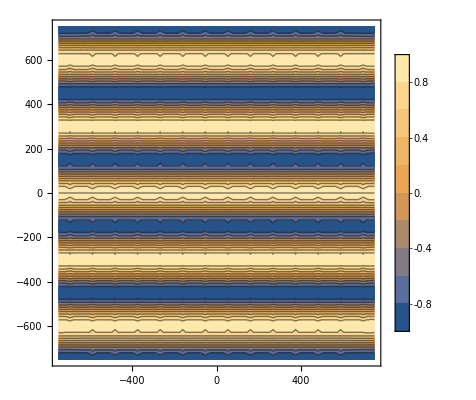

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->6*)(*,PlotPoints->20*)]
```

```mathematica
(*ClearAll[b]*)
```

Below I use the definition of u0d.

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[2,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero. 
Note, if too many modes are used for the noise, Mathematica can’t solve this differential equation.

```mathematica
uofρRule=DSolve[{D[u[ρ,x,y],{ρ}]==-u[ρ,x,y]^2(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},u,{ρ,x,y}]//Flatten;
c1Rule=Solve[C[1][x,y]==0(*uofρRule[[1,2]][1,x,y]==1*),C[1][x,y]]//Flatten;
uofρ=u/.uofρRule/.c1Rule//N
```

Function[{ρ,x,y},-(1. ρ)/(0.-1. Hypergeometric2F1[-0.333333,0.5,0.666667,-1. ρ^3 Cos[0.020944 y]^2])]

```mathematica
rofρRule=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρRule/.c1Rule//N
```

Function[{ρ,x,y},Hypergeometric2F1[-0.333333,0.5,0.666667,-1. ρ^3 Cos[0.020944 y]^2]/ρ+0.]

```mathematica
uofρ=Function[{ρ,x,y},rofρ[ρ,x,y]^-1]
```

Function[{ρ,x,y},1/rofρ[ρ,x,y]]

!!! The two constant of integration in uofρ and rofρ are not the same !!!

```mathematica
(*c1Rule=Solve[uofρ[1,x,y]==1,C[1][x,y]]//Flatten;*)
```

```mathematica
c1Rule
```

{C[1][x,y]→0}

```mathematica
rofρRule[[2]][b^-1,x,y]/.c1Rule
```

Hypergeometric2F1[-1/3,1/2,2/3,-Cos[(π y)/150]^2]

```mathematica
Plot3D[uofρRule[[1,2]][b^-1,x,y]/.c1Rule,{y,yMin,yMax},{x,yMin,yMax}]
```

-Graphics3D-

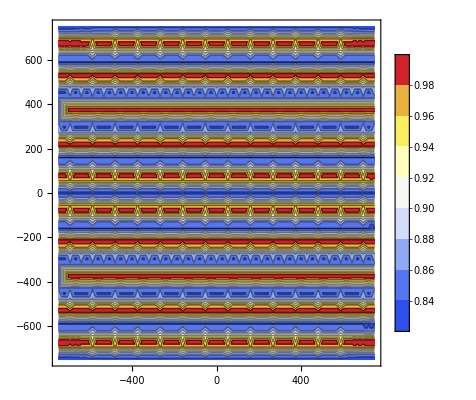

```mathematica
ContourPlot[uofρ[b,x,y]/.c1Rule,{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap"(*,MaxRecursion->5*)(*,PlotPoints->20*)]
```

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->uofρ[ρ,x,y](*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&;
AExpOfρ
```

1/ρ^2+(2. ξ[t,x,y])/ρ+(ξ[t,x,y]^2-2 ξ^(1,0,0)[t,x,y])+(1. a3[t,0,x,y]+0.5 Cos[0.020944 y]^2) ρ+O[ρ]^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b(*[x,y]*) ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-ρ-ρ Cos[(π y)/150]^2

Let' s look for ξ

```mathematica
xiRule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  ξ[t,x,y]]//Flatten
```

{ξ[t,x,y]→0.}

```mathematica
(*xiRule=ξ[t,x,y]->-(1.-1. Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,1. (-0.000811429315297694 Cos[2.7019354914839884+0.05445427266222308 x+0.24294983187761068 y]^2-1. (0.19999999999999998 Cos[5.772098284647657+0.050265482457436686 x+0.12147491593880531 y]+Cos[0.020943951023931956 y])^2)]);*)
```

```mathematica
Solve[SeriesCoefficient[AExpOfρ,{ρ,0,0}]==SeriesCoefficient[AToMatch,{ρ,0,0}]]
```

{{ξ^(1,0,0)[t,x,y]→1/2 ξ[t,x,y]^2}}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
3000/10/24//N
```

12.5

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-1. (1.+1.5 Cos[0.020944 y]^2)}

From Chasler paper a3 should be

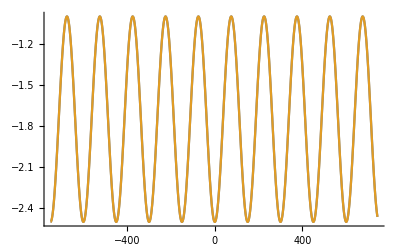

```mathematica
Plot[{-1/2 b^3(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,yValues[[1]],yValues[[-1]]}]
```

Export a3 Initial data

```mathematica
(*a3PertAmpl=10^-4;
a3Pert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤150,l++,
{AAa3,ϕna3,nxa3,nya3}={RandomReal[a3PertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
a3Pert=Table[a3Pert[[i,j]]+AAa3 Cos[ϕna3+(2π)/(xMax-xMin)nxa3 xValues[[i]]+(2π)/(xMax-xMin)nya3 yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]*)
```

```mathematica
(*Max[a3Pert]
Max[Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]]),{i,1,xValues//Length},{j,1,yValues//Length}]]*)
```

0.00227982

-1.

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*+a3Pert[[i,j]]*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
xiData=Table[(ξ[t,x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.xiRule/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessData=Table[N[(uofρRule[[1,2]][b^-1,x,y])^-1/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]],prec]1,{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessData[[1,1]]
```

1.199314370356943020927941784000363163729331729667536501210167372

```mathematica
ListContourPlot[a3Data]
```

-Graphics-

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10Initiala3_BBB.h5

```mathematica
Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10Initialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10Initialguess_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

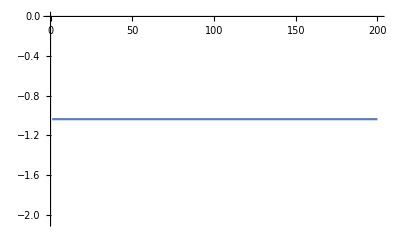

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"][[1,;;,10]],Joined->True,PlotRange->All]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,x,y]+Derivative[0,1,0][ξ][t,x,y]+1/4(-4 f1[t,x,y] ξ[t,x,y](*+3 𝒢^(0,0,1)[t,x,y]*)(*+3 𝒫^(0,1,0)[t,x,y]*))u^2;
```

```mathematica
FExpOfρ=FExp/.u->uofρ[ρ,x,y](*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,2}]&
```

ξ^(0,1,0)[t,x,y]+1. f1[t,x,y] ρ-1. (f1[t,x,y] ξ[t,x,y]) ρ^2+O[ρ]^3

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

```mathematica
SeriesCoefficient[FExpOfρ,{ρ,0,1}]
SeriesCoefficient[FToMatch,{ρ,0,1}]
```

1. f1[t,x,y]

0

Chasler paper

```mathematica
FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y]
```

-ρ Cos[(π y)/150] √(1+Cos[(π y)/150]^2)

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,1}]==SeriesCoefficient[FExpOfρ,{ρ,0,1}]
```

-Cos[(π y)/150] √(1+Cos[(π y)/150]^2)==1. f1[t,x,y]

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,x,y]]//Simplify
```

{{f1[t,x,y]→-1. Cos[0.020944 y] √(1.+Cos[0.020944 y]^2)}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
1500
```

1500

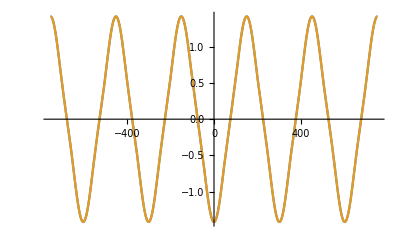

```mathematica
Plot[{- b^3 u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,0}]
SeriesCoefficient[FExpOfρ,{ρ,0,0}]
```

0

ξ^(0,1,0)[t,x,y]

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,2}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},0.]}

ξ can’t depend on x!

Export fx initial data

```mathematica
(*Maxfx=Maximize[fxRule[[1,1,2]],y][[1]];*)
```

```mathematica
fxPertAmpl=10^-3;
fxPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤150,l++,
{AAfx,ϕnfx,nxfx,nyfx}={RandomReal[fxPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fxPert=Table[fxPert[[i,j]]+AAfx Cos[ϕnfx+(2π)/(xMax-xMin)nxfx xValues[[i]]+(2π)/(xMax-xMin)nyfx yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]
```

```mathematica
fxData=Table[((f1[t,x,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])+fxPert[[i,j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
fxData//Dimensions
```

{200,200}

```mathematica
Max[fxPert]/Max[Table[((f1[t,x,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]]),{i,1,xValues//Length},{j,1,yValues//Length}]]
```

0.0131569

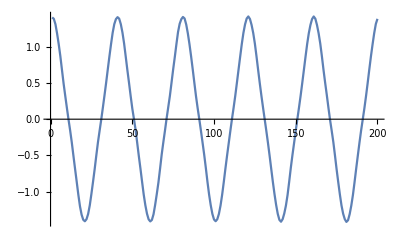

```mathematica
ListPlot[fxData[[1]],Joined->True]
```

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10Initialfx_BBB.h5

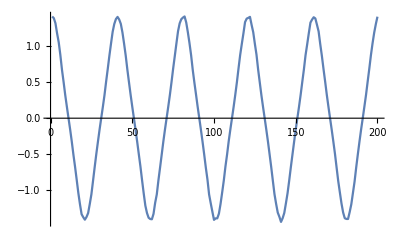

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"][[1,1]],Joined->True,PlotRange->All]
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->uofρ[ρ,x,y]^1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
fyRule[[1,1,2]]/.x->148/.y->-50000
fyRule[[1,1,2]]/.x->148/.y->50000
```

0.

0.

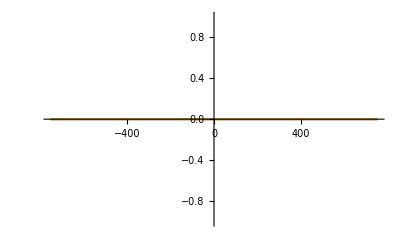

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyPertAmpl= 10^-3;
fyPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤100,l++,
{AAfy,ϕnfy,nxfy,nyfy}={RandomReal[fyPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fyPert=Table[fyPert[[i,j]]+AAfy Cos[ϕnfy+(2π)/(xMax-xMin)nxfy xValues[[i]]+(2π)/(yMax-yMin)nyfy yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]
```

```mathematica
fyData=Table[((f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])1+fyPert[[i,j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
Max[fyData]
```

0.0154315

```mathematica
Norm[fyData]
```

0.185001

```mathematica
0.006967497791432687
```

0.0069675

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{200,200}

```mathematica
ListContourPlot[fyData]
```

-Graphics-

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
(*ClearAll[uofρ]*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ/.c1Rule[[1]](*/.ξ->Function[{t,x,y},0]*)/.ρ->ρs/.x->xs/.y->ys]*)
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]*)
```

Horizon location

```mathematica
rofρ2=r/.DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+((*b[x,y]*)b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2)),r[1,x,y]==1},r,{ρ,x,y}]//Flatten
```

{Function[{ρ,x,y},(ρ-ρ Hypergeometric2F1[-1/3,1/2,2/3,-Cos[(π y)/150]^2]+Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3 Cos[(π y)/150]^2])/ρ]}

```mathematica
Plot3D[uofρ[b^-1,x,y](*/.b[x,y]->1*)/.c1Rule,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Maximize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
Minimize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
```

1.

0.83381

```mathematica
Maximize[rofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
Minimize[rofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
```

1.19931

1.

```mathematica
1/0.8338097372270935
```

1.19931

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
ρofu[MyGrid[[2,1,1,1]]]//N//AbsoluteTiming
```

{0.011216,0.771302}

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
ρofuValues=ParallelTable[ρofu[MyGrid[[n,i,j,k]]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{960.147,Null}

```mathematica
123
```

123

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.194608,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.033244,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{41.2656,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*(1+10^-4( RandomReal[]-0.5))*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{1611.04,Null}

```mathematica
InitialB=ParallelTable[N[-1/2 Log[(1+(b ρofuValues[[n,ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[n,ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[n,ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1,1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{13.2508,Null}

```mathematica
(*Table[InitialB[[1,i,j]]=-u1d[xValues[[i]],yValues[[j]]]^2/2,{i,1,xValues//Length},{j,1,yValues//Length}];*)
```

```mathematica
(*ListContourPlot[InitialB[[1]],PlotLegends->Automatic]*)
```

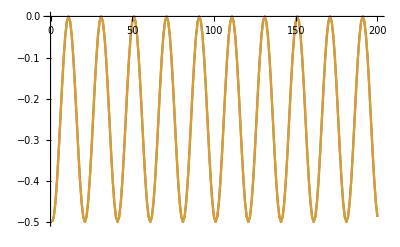

```mathematica
ListPlot[{InitialB[[1,1,1,;;]],
Table[-u1d[xValues[[1]],yValues[[i]]]^2/2(*-InitialB[[1,1,i]]*),{i,1,yValues//Length}]},Joined->True(*,PlotStyle->{Dashed,Dotted}*),PlotRange->All]
```

```mathematica
(*phiFunc=InterpolatingFunction[…]*)
```

```mathematica
(*phi=Table[phiFunc[uValues[[i]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];*)
```

```mathematica
(*ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming*)
```

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
(*AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming*)
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->InitialB[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.00002,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10InitialB_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"][[1,1]]//ListPlot3D
```

-Graphics3D-

#### B2 Function

```mathematica
Maxg=FindMaxValue[{Abs[InterpolatingFunction[…][z]//Re],0<=z<=1},z];
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

InterpolatingFunction::dmval: Input value {-0.0000320803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0000260249} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt-ArcTan[u]/2+1/4 Log[1-u]-1/4 Log[1+u]))/.ω->4.763570116920460863I
```

```mathematica
Parametricgxy[u_]:=1/20 ExpOfHxy[0,u]InterpolatingFunction[…][u]/Maxg//Re;
```

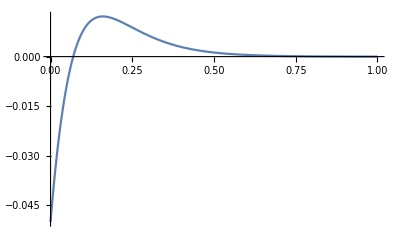

```mathematica
Plot[Parametricgxy[u],{u,0,1},PlotRange->All]
```

```mathematica
Series[-Log[(1-4 a^2 u^8)^(1/6)]/u^4,{u,0,4}]
```

(2 a^2 u^4)/3+O[u]^5

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==2 u^2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}]/. C[1]->0/. C[2]->0/.C[3]->0
```

{{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4}}

```mathematica
InitialB2=ParallelTable[N[-Log[(1-4 a^2 u^8)^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {1.015336064422973428250209655053370564795775271193209696481386153} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0^4 encountered.

InterpolatingFunction::dmval: Input value {1.036510628643730816574907509074508115619754151458133288870865591} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {1.055142258140883961408220202193907379117544546064782024151121863} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0^4 encountered.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{110.765,Null}

```mathematica
InitialB2uzero=ParallelTable[0,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.19716,Null}

```mathematica
InitialB2[[1]]=InitialB2uzero;
```

```mathematica
ExportDataB2=Join[{InitialB2(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB2(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

Part::take: Cannot take positions 1 through 24 in {{{0, <<98>>, 0}, <<99>>}, {<<100>>}}.

Part::take: Cannot take positions 24 through 35 in {{{0, <<98>>, 0}, <<99>>}, {<<100>>}}.

{0.195505,Null}

```mathematica
ExportAttributesB2=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataB2=Table[ExportAttributesB2[[i]]->ExportDataB2[[i]],{i,1,ExportAttributesB2//Length}];//AbsoluteTiming
```

{0.000023,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5

#### G Function

```mathematica
ArcSinh[(b^3 u1 u2 ρ^3)/(√(1+b^3 (u1^2+u2^2) ρ^3))]//TrigToExp//Together//Simplify
```

Log[(u1 u2 ρ^3)/(√(1+(u1^2+u2^2) ρ^3))+√(1+(u1^2 u2^2 ρ^6)/(1+(u1^2+u2^2) ρ^3))]

```mathematica
InitialG=ParallelTable[N[ArcSinh[(b^3 u1Values[[xi,yi]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3)/(√(1+b^3 (u1Values[[xi,yi]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))](*Log[(b^3 u1Values[[n,ui]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3+√((1+b^3 uValues[[n,ui]]^2 ρofuValues[[n,ui,xi,yi]]^3) (1+b^3 u2Values[[xi,yi]]^2 ρofuValues[[n,ui,xi,yi]]^3)))/(√(1+b^3 (uValues[[n,ui]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))]*)uValues[[n,ui]]^-3,$MinPrecision](*+((RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{12.4495,Null}

```mathematica
InitialGAnalytic[u_,x_,y_]:=ArcSinh[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3)/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))](*Log[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3+√((1+b^3 u1d[x,y]^2 ρofu[{u,x,y}]^3) (1+b^3 u2d[x,y]^2 ρofu[{u,x,y}]^3)))/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))]*)u^-3;
```

```mathematica
InitialG1=ParallelTable[N[SeriesCoefficient[InitialGAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*+( (RandomReal[]-0.5)/10^4)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.67622,Null}

```mathematica
InitialG[[-1,-1,;;,;;]]//ListPlot3D
```

-Graphics3D-

```mathematica
InitialG[[1,1]]=InitialG1;
```

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->(InitialG[[i]]//Re),{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.2786,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN150q6InitialG_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10InitialG_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN200q10InitialG_BBB.h5